# Tarea 2

## Pregunta 1.b

Se tiene que mediante la función FindReduce, podemos encontrar una de todas las soluciones que satisfacen las siguientes desigualdades, el cual están dados por

```mathematica
FindInstance[{x+y+z≥1,-x-5y-Sqrt[5]z≥1,-x-10y-Sqrt[10]z≥1,-x-20y-Sqrt[20]z≥1,-x-40y-Sqrt[40]z≥1,x+80y+Sqrt[80]z≥1},{x,y,z},Integers]
```

{{x→51,y→3,z→-31}}

Por lo tanto, el hiperplano esta dado por:

```mathematica
H[x_,y_]:=51+3*x-31*y
```

Cuya representación gráfica esta dada por:

```mathematica
Show[Plot3D[{51+3*x-31*y},{x,0,80},{y,0,10}],
ListPointPlot3D[{{1,1,1},{5,Sqrt[5],-1},{10,Sqrt[10],-1},
{20,Sqrt[20],-1},{40,Sqrt[40],-1},{80,Sqrt[80],1}}]]
```

-Graphics3D-

Claramente, el hiperplano satisface que

```mathematica
51+3*1-31*Sqrt[1]
```

23

```mathematica
51+3*5-31*Sqrt[5]//N
```

-3.31811

```mathematica
51+3*10-31*Sqrt[10]//N
```

-17.0306

```mathematica
51+3*20-31*Sqrt[20]//N
```

-27.6362

```mathematica
51+3*40-31*Sqrt[40]//N
```

-25.0612

```mathematica
51+3*80-31*Sqrt[80]//N
```

13.7276

Por lo tanto, el hiperplano satisface la propiedad dicha del teorema usado.

## Pregunta 1.c

Mediante la optimización numerica, se tiene que

```mathematica
NMinimize[{(1/2)*Norm[{y,z}]^2,x+y+z≥1,-x-5y-Sqrt[5]z≥1,-x-10y-Sqrt[10]z≥1,-x-20y-Sqrt[20]z≥1,-x-40y-Sqrt[40]z≥1,x+80y+Sqrt[80]z≥1},{x,y,z}]
```

{2.90568,{x→3.15738,y→0.241202,z→-2.39858}}

Cuyo hiperplano esta dado por:

```mathematica
Show[Plot3D[{3.157378652621899+0.24120226605671236*x+-2.3985809184293134*y},{x,0,80},{y,0,10}],
ListPointPlot3D[{{1,1,1},{5,Sqrt[5],-1},{10,Sqrt[10],-1},
{20,Sqrt[20],-1},{40,Sqrt[40],-1},{80,Sqrt[80],1}}]]
```

-Graphics3D-

## Pregunta 1.d

```mathematica
3.157378652621899+0.24120226605671236*1+-2.3985809184293134*Sqrt[1]
```

1.

```mathematica
3.157378652621899+0.24120226605671236*5+-2.3985809184293134*Sqrt[5]
```

-1.

```mathematica
3.157378652621899+0.24120226605671236*10+-2.3985809184293134*Sqrt[10]
```

-2.01558

```mathematica
3.157378652621899+0.24120226605671236*20+-2.3985809184293134*Sqrt[20]
```

-2.74536

```mathematica
3.157378652621899+0.24120226605671236*40+-2.3985809184293134*Sqrt[40]
```

-2.36449

```mathematica
3.157378652621899+0.24120226605671236*80+-2.3985809184293134*Sqrt[80]
```

1.

## Pregunta 2

Graficamos los puntos asociados a los puntos (FPR,TPR), se tiene que:

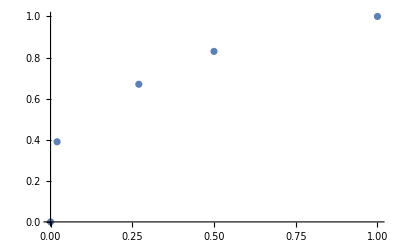

```mathematica
ListPlot[{{0,0},{1,1},{0.5,0.83},{0.27,0.67},{0.02,0.39}}]
```

Por lo tanto, mediante la siguiente función definida a funciones lineales, podemos “representar” la curva mediante la siguiente función:

```mathematica
g[x]=Piecewise[{{19.5x,0≤ x<0.02},{1.12x+0.3676,0.02≤ x<0.27},{0.695652x+0.482174,0.27≤ x<0.5},{0.34x+0.66,0.5≤ x≤ 1}}]
```

Piecewise[{{19.5 x, 0≤x<0.02}, {0.3676+1.12 x, 0.02≤x<0.27}, {0.482174+0.695652 x, 0.27≤x<0.5}, {0.66+0.34 x, 0.5≤x≤1}, {0, True}}]

Cuya representación en el gráfico cartesiano, esta dado por:

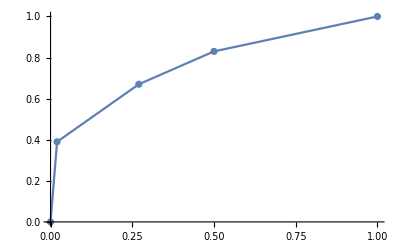

```mathematica
Show[Plot[g[x],{x,0,1}],ListPlot[{{0,0},{1,1},{0.5,0.83},{0.27,0.67},{0.02,0.39}}]]
```

Y cuya integración esta dada por:

```mathematica
Integrate[g[x],{x,0,1}]
```

0.7664